# ЛР1. Актуализация знаний 1-ого семестра.

## 1. Работаем со списками и элементарными вычислениями.

### 1.1

Докажите эмпирически (с помощью вычислений) сходимость числового ряда ∑_(n=0)^∞ (-1)^n/(2n+1).  Сделайте предположение о том, к какому числу сходится ряд. Подтвердите вычисления графически.

```mathematica
(*Члены последовательности от 0 до n-го:*)
n:=50;
(-1)^#/(2#+1)&/@Range[0,n]
```

{1,-1/3,1/5,-1/7,1/9,-1/11,1/13,-1/15,1/17,-1/19,1/21,-1/23,1/25,-1/27,1/29,-1/31,1/33,-1/35,1/37,-1/39,1/41,-1/43,1/45,-1/47,1/49,-1/51,1/53,-1/55,1/57,-1/59,1/61,-1/63,1/65,-1/67,1/69,-1/71,1/73,-1/75,1/77,-1/79,1/81,-1/83,1/85,-1/87,1/89,-1/91,1/93,-1/95,1/97,-1/99,1/101}

```mathematica
(*Их сумму могу посчитать с помощью Total:*)
(-1)^#/(2#+1)&/@Range[0,n]//Total//N
```

0.7903

```mathematica
(*Все суммы от 0 членов:*)
Sum[(-1)^i/(2i+1),{i,0,#}]&/@Range[0,10]
(*Или из палитры:*)
∑_(i=0)^# (-1)^i/(2i+1)&/@Range[0,10]
```

{1,2/3,13/15,76/105,263/315,2578/3465,36979/45045,33976/45045,622637/765765,11064338/14549535,11757173/14549535}

{1/2,1/4,5/12,7/24,47/120,37/120,319/840,533/1680,1879/5040,1627/5040,20417/55440}

```mathematica
(*Приближенные суммы числового ряда называются частичными суммами числового ряда. Сумма из n первых членов числового ряда называется n-й суммой ряда. Попробую посчитать предел*)
Limit[Sum[(-1)^i/(2i+1),{i,0,im}],im->Infinity]
```

π/4

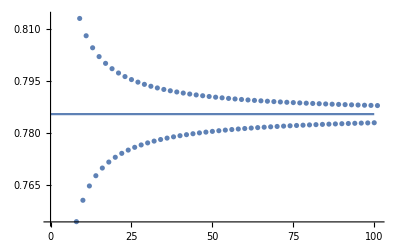

```mathematica
pl1=ListPlot[Sum[(-1)^i/(2i+1),{i,0,#}]&/@Range[0,100]];
pl2=Plot[{Pi/4},{x,0,100}, Axes->True];
Show[pl1,pl2]
(*Из графика видно, что сходится к значению, посчитанному выше: Pi/4*)
```

### 1.2

Докажите эмпирически расходимость  ряда. ∑_(n=1)^∞ 1/n. Для этого можно доказать, что для любого числа K, существует N, такое что ∑_(n=1)^N 1/n> K.

### Пример

```mathematica
1/(#!)&/@Range[0,30](*Первый 31 член ряда*)
```

{1,1,1/2,1/6,1/24,1/120,1/720,1/5040,1/40320,1/362880,1/3628800,1/39916800,1/479001600,1/6227020800,1/87178291200,1/1307674368000,1/20922789888000,1/355687428096000,1/6402373705728000,1/121645100408832000,1/2432902008176640000,1/51090942171709440000,1/1124000727777607680000,1/25852016738884976640000,1/620448401733239439360000,1/15511210043330985984000000,1/403291461126605635584000000,1/10888869450418352160768000000,1/304888344611713860501504000000,1/8841761993739701954543616000000,1/265252859812191058636308480000000}

```mathematica
1/(#!)&/@Range[0,30]//Total//N[#,30]&(*Частичная сумма первых 31 члена*)
```

2.71828182845904523536028747135

```mathematica
ⅇ-(1/(#!)&/@Range[0,30]//Total//N[#,30]&)(*Предполагаем, что ряд сходится к экпоненте*)
```

0.

```mathematica
Table[Abs[ⅇ-(1/(#!)&/@Range[0,i]//Total)],{i,1,30}]//N[#,50]&(*смотрим, как погрешность изменяется с увеличением количества членов ряда*)
```

{0.71828182845904523536028747135266249775724709369996,0.21828182845904523536028747135266249775724709369996,0.051615161792378568693620804685995831090580427033293,0.0099484951257119020269541380193291644239137603666262,0.0016151617923785686936208046859958310905804270332929,0.00022627290348967980473191579710694220169153814440402,0.000027860205076981392033503098694243788993125445991321,3.0586177753940904462015113926564874058238586897337×10^-6,3.0288585299550138094577947025789834056812676733511×10^-7,2.7312660755642474420206278018039434042553575095249×10^-8,2.2605523702007556451541696325977152675014667098074×10^-9,1.7287667141394574723316060047757203624712434435396×10^-10,1.2286233045729601239236828776022556919867239319076×10^-11,8.1548744799987652538513079734045125363458895944194×10^-13,5.0771074817894877795017598761644209219078935466305×10^-14,2.9763014940210248206355238504687689431095589678282×10^-15,1.6484423967550405743657826745844892687606623262366×10^-16,8.6521699896417928144146239578755926408721917789627×10^-18,4.3153474301746309745864272100331189165145278713657×10^-19,2.0502980686246611610843659159697854190415837545263×10^-20,9.3003962285535037999608478619242383512836375520102×10^-22,4.0360483610293051321195041942177000797114946561826×10^-23,1.6787819039862109440259226269488775653215200992528×10^-24,6.7044332890092594977209322147705763996793996645543×10^-26,2.5748300462478610152607899556588919438049525412535×10^-27,9.5233783023063555185846409810935326382296998780863×10^-29,3.396884385108093701589241446196192403680126837431×10^-30,1.1699514803825579143719971888408047587238141087988×10^-31,3.8955191737786221216120731146973059479763961712231×10^-33,1.2553154496271647775915158905120028382956234760113×10^-34}

### Решение.

```mathematica
(*Посмотрю первые 50 членов ряда*)
1/#&/@Range[1,50]
```

{1,1/2,1/3,1/4,1/5,1/6,1/7,1/8,1/9,1/10,1/11,1/12,1/13,1/14,1/15,1/16,1/17,1/18,1/19,1/20,1/21,1/22,1/23,1/24,1/25,1/26,1/27,1/28,1/29,1/30,1/31,1/32,1/33,1/34,1/35,1/36,1/37,1/38,1/39,1/40,1/41,1/42,1/43,1/44,1/45,1/46,1/47,1/48,1/49,1/50}

```mathematica
(*Посмотрел. Посчитаю частичную сумму первых 50 членов ряда*)
1/#&/@Range[1,50]//Total//N
(*//N[#,20]& для точности*)
```

4.49921

```mathematica
(*Пускай, наверное, ряд сходится к 4.5*)
4.5-(1/#&/@Range[1,50]//Total//N)
```

0.000794662

```mathematica
(*Но можно посчитать больше членов ряда, он не стремится к 4.5*)
1/#&/@Range[1,60]//Total//N
```

4.67987

```mathematica
(*Cмотрю, как погрешность изменяется с увеличением количества членов ряда*)
Table[Abs[4.5-(1/#&/@Range[1,i]//Total)],{i,1,60}]
(*Сначала стремилась к нулю, а потом снова стала возрастать после суммы первых 50 членов*)
```

{3.5,3.,2.66667,2.41667,2.21667,2.05,1.90714,1.78214,1.67103,1.57103,1.48012,1.39679,1.31987,1.24844,1.18177,1.11927,1.06045,1.00489,0.95226,0.90226,0.854641,0.809187,0.765708,0.724042,0.684042,0.64558,0.608543,0.572829,0.538346,0.505013,0.472755,0.441505,0.411202,0.38179,0.353219,0.325441,0.298414,0.272098,0.246457,0.221457,0.197067,0.173257,0.150001,0.127274,0.105052,0.0833128,0.0620362,0.0412028,0.0207947,0.000794662,0.0188132,0.038044,0.0569119,0.0754304,0.0936122,0.111469,0.129013,0.146255,0.163204,0.17987}

## 2. Пишем собственные функции.

### Вычисление числа π методом Монте-Карло. Теория.

Идея метода в случайном распределении точек. Зададим некоторое количество случайных точек в квадрате 0 ≤ x ≤ 1, 0 ≤ y ≤ 1.

```mathematica
Short[pts=RandomReal[{0,1},{1000,2}]]
```

{{0.199095,0.331074},{0.373106,0.39224},«996»,{0.670427,0.553998},{0.807449,0.744632}}

Очевидно, что геометрически точки будут лежать внутри квадарата со строной 1. Если вписать в этот квадрат окружность, то логично, что часть точек окажется в ней.

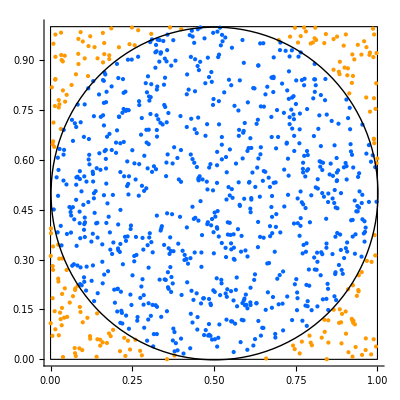

Далее логично предположить, что отношение площадей фигур будет “равно” или, лучше сказать, “близко”, отношению количества точек внутри каждой фигуры. 
Тогда если K - это количество точек в круге, а N - общее количество точек  (лежащих в квадрате), то K/N=S_круга/S_квадарата. 
Площади круга и квадарта мы можем вычислить. S_круга=π*1/4, S_квадрата=1.  
Получаем финальное соотношение, откуда выражаем π. π = 4 * K/N.

Остаётся только найти количечество точек внутри окружности исходя из геометрических свойств. С увеличением количества точек, ожидаем увеличение точности.

### 2.1

Реализуйте функцию для вычисления числа π методом Монте-Карло. На вход функция принимает, количество точек. Исследуйте, как меняется точность вычислений с увеличением количества точек.

### Решение.

```mathematica
GetPi[n_]:=(4*Length[Select[RandomReal[{0,1},{n,2}],(#[[1]]-0.5)^2+(#[[2]]-0.5)^2<=0.5^2&]])/n
```

```mathematica
(*Проверяю*)
n1=100;
n2=1000;
n3=10000;
n4=100000;
n5=1000000;
GetPi[n1]//N
GetPi[n2]//N
GetPi[n3]//N
GetPi[n4]//N
GetPi[n5]//N
```

3.16

3.196

3.1176

3.136

3.14188

```mathematica
Manipulate[GetPi[a],{a,1,10000}]
```

## 3. Вспоминаем графические примитивы.

Модифицируйте функцию из задания 2.1 таким образом, чтобы она также возвращала графическую визуализацию работы метода.

### Решение.

```mathematica
showPoints[n_]:=Graphics[{Thick,Line[{{0,0},{0,1},{1,1},{1,0},{0,0}}],Thick,Circle[{0.5,0.5},0.5],Hue[0.07,0.9,0.84],Point[Select[RandomReal[{0,1},{n,2}],(#[[1]]-0.5)^2+(#[[2]]-0.5)^2>=0.5^2&]],Hue[0.65,0.86,0.76],Point[Select[RandomReal[{0,1},{n,2}],(#[[1]]-0.5)^2+(#[[2]]-0.5)^2<=0.5^2&]]},PlotRange->{{0,1},{0,1}},Axes->True]
showOnlyPoints[n_]:=Graphics[{Hue[0.07,0.9,0.84],Point[Select[RandomReal[{0,1},{n,2}],(#[[1]]-0.5)^2+(#[[2]]-0.5)^2>=0.5^2&]],Hue[0.65,0.86,0.76],Point[Select[RandomReal[{0,1},{n,2}],(#[[1]]-0.5)^2+(#[[2]]-0.5)^2<=0.5^2&]]},PlotRange->{{0,1},{0,1}},Axes->True]
```

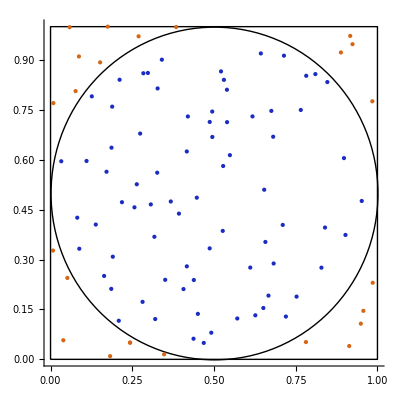

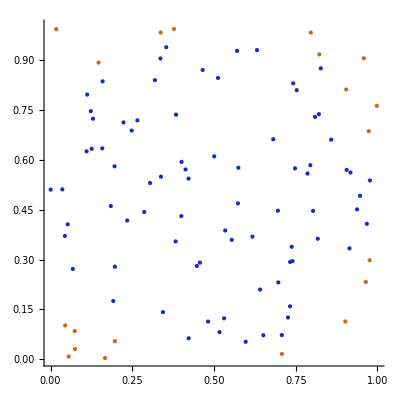

```mathematica
showPoints[n1]
showOnlyPoints[n1]
```

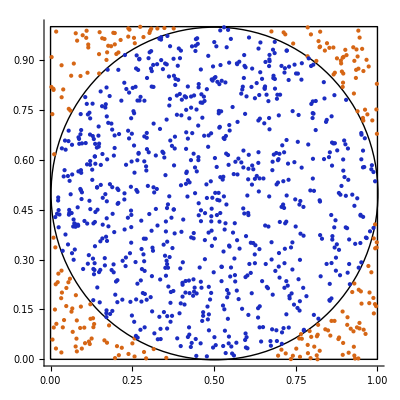

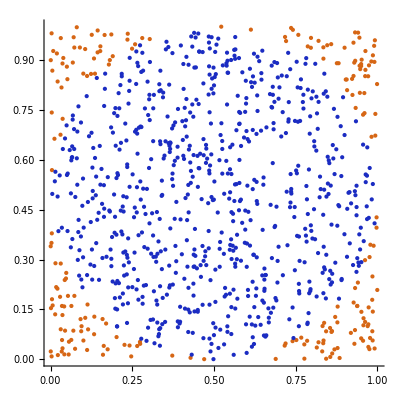

```mathematica
showPoints[n2]
showOnlyPoints[n2]
```

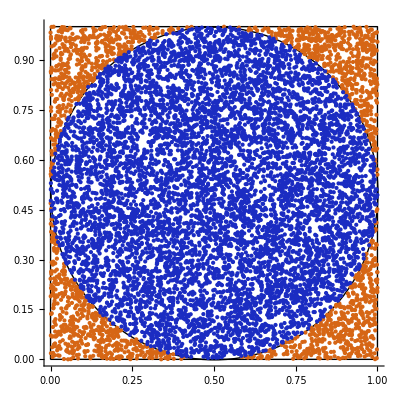

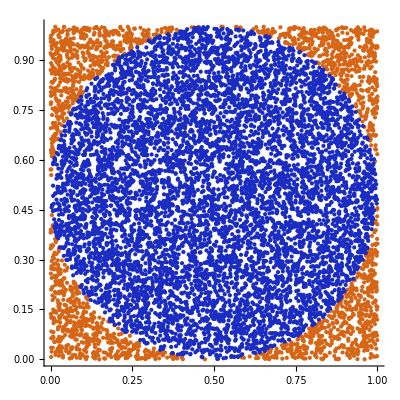

```mathematica
showPoints[n3]
showOnlyPoints[n3]
```

```mathematica
Manipulate[showPoints[a],{a,1,5000}]
```

```mathematica
Manipulate[showOnlyPoints[a],{a,1,5000}]
```

## 4. Динамические вычисления.

### 4.1.

Реализуйте функцию, принимающую на вход полином и возвращающую все его корни, а также графическую интерпретацию действительных корней.

### Пример.

Пусть задано уравнение.

```mathematica
eqn = x^7+7 x^3+x^2+11==0
```

11+x^2+7 x^3+x^7==0

```mathematica
eqn//Solve//Values//N//Flatten 
(*Получили корни*)
```

{-1.12547,-1.14624-1.26951 ⅈ,-1.14624+1.26951 ⅈ,0.455814-1.03462 ⅈ,0.455814+1.03462 ⅈ,1.25316-1.0214 ⅈ,1.25316+1.0214 ⅈ}

```mathematica
rootsreal=eqn//Solve//Values//N//Flatten//Cases[#,_Real]&
(*Вот так можно получить дествительные корни*)
```

{-1.12547}

Для получение визуализации лучше использовать функцию Plot с опцией Epilog.

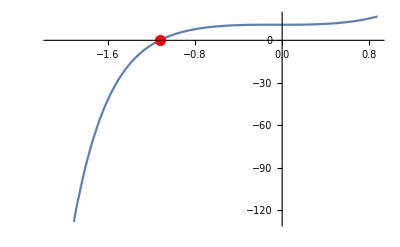

### Решение.

```mathematica
eqn1 = x^7+7 x^3+x^2+11==0
eqn2=x^8+x^4+1==0
eqn3=x^3+6 x^2-9x==0
eqn4=x^5-2 x^4+x^3-x^2-2x+1==0
```

11+x^2+7 x^3+x^7==0

1+x^4+x^8==0

-9 x+6 x^2+x^3==0

1-2 x-x^2+x^3-2 x^4+x^5==0

```mathematica
(*Функция,принимающую на вход полином и возвращающая все его корни*)
getPolyRoots[poly_]:=poly//Solve//Values//N//Flatten 
(*Функция,принимающую на вход полином и возвращающая все его действительные корни*)
getPolyRootsReal[poly_]:=poly//Solve//Values//N//Flatten //Cases[#,_Real]&
```

```mathematica
(*Проверяю:*)
getPolyRoots[eqn1]
getPolyRootsReal[eqn1]
```

{-1.12547,-1.14624-1.26951 ⅈ,-1.14624+1.26951 ⅈ,0.455814-1.03462 ⅈ,0.455814+1.03462 ⅈ,1.25316-1.0214 ⅈ,1.25316+1.0214 ⅈ}

{-1.12547}

```mathematica
getPolyRoots[eqn2]
getPolyRootsReal[eqn2]
```

{-0.866025-0.5 ⅈ,0.866025+0.5 ⅈ,-0.5-0.866025 ⅈ,0.5+0.866025 ⅈ,0.5-0.866025 ⅈ,-0.5+0.866025 ⅈ,0.866025-0.5 ⅈ,-0.866025+0.5 ⅈ}

{}

```mathematica
getPolyRoots[eqn3]
getPolyRootsReal[eqn3]
```

{0.,-7.24264,1.24264}

{0.,-7.24264,1.24264}

```mathematica
getPolyRoots[eqn4]
getPolyRootsReal[eqn4]
```

{-0.836401,0.423098,1.95057,0.231366-1.18118 ⅈ,0.231366+1.18118 ⅈ}

{-0.836401,0.423098,1.95057}

```mathematica
(*Функция для графической визуализации действительных корней полинома*)
showPolyRootsReal[poly_]:=Plot[poly,{x,-10,10},Epilog->{PointSize[Medium],RGBColor[0.5,0.03,0.5],Point[{#,0}&/@Cases[Flatten[N[Values[Solve[poly]]]],_Real]]},PlotRange->{{-10,10},{-10,10}}]
```

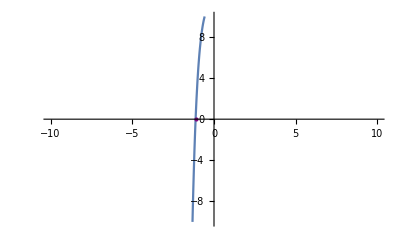

```mathematica
(*Проверяю*)
showPolyRootsReal[eqn1]
```

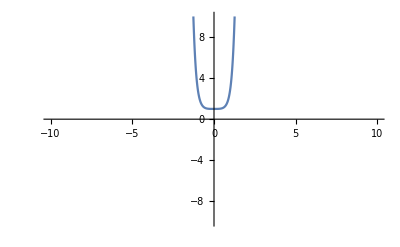

```mathematica
showPolyRootsReal[eqn2]
```

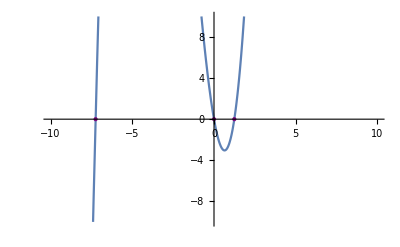

```mathematica
showPolyRootsReal[eqn3]
```

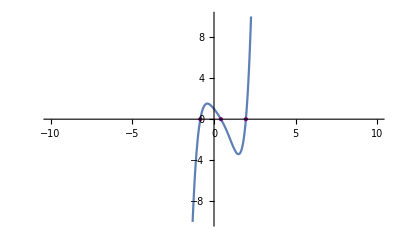

```mathematica
showPolyRootsReal[eqn4]
```

### 4.2

Реализуйте с помощью функции Manipulate скрипт аналогичный предыдущему. Теперь один из коэффициентов полинома - параметр. Продемонстируйте изменения графической интерпретации при изменении параметра.

### Решение.

```mathematica
eqn5=x^7+7 x^3+a*x^2+11==0
eqn6=a*x^3+6 x^2-9x==0
eqn7=-a*x^5-2 x^4-a*x^3-a*x^2-2x+1==0
```

11+a x^2+7 x^3+x^7==0

-9 x+6 x^2+a x^3==0

1-2 x-a x^2-a x^3-2 x^4-a x^5==0

```mathematica
(*Функция,принимающую на вход полином и возвращающая все его корни, их изменения в зависимости от параметра*)
getPolyParametricRoots[poly_]:=Manipulate[poly//Solve//Values//N//Flatten ,{a,-10,10}]
(*Функция,принимающую на вход полином и возвращающая все его действительные корни, их изменения в зависимости от параметра*)
getPolyParametricRootsReal[poly_]:=Manipulate[poly//Solve//Values//N//Flatten //Cases[#,_Real]&,{a,-10,10}]
```

```mathematica
(*Проверяю*)
getPolyParametricRoots[eqn5]
getPolyParametricRootsReal[eqn5]
```

```mathematica
getPolyParametricRoots[eqn6]
getPolyParametricRootsReal[eqn6]
```

```mathematica
getPolyParametricRoots[eqn7]
getPolyParametricRootsReal[eqn7]
```

```mathematica
(*Функция, показывающая изменения графической интерпритации при изменении параметра*)
showPlotChanges[poly_]:=Manipulate[Plot[poly,{x,-10,10},Epilog->{PointSize[Medium],RGBColor[0.5,0.03,0.5],Point[{#,0}&/@Cases[Flatten[N[Values[Solve[poly]]]],_Real]]},PlotRange->{{-10,10},{-10,10}}],{a,-10,10}]
```

```mathematica
showPlotChanges[eqn5]
```

```mathematica
showPlotChanges[eqn6]
```

```mathematica
showPlotChanges[eqn7]
```

### 4.3

Реализуйте функцию принимающую на вход полином и возвращающую все его корни, а также графическую интерпретацию комплексных корней. Комплексные корни стоит отрисовать на комплексной плоскости.  Подпишите их.

### Решение.

```mathematica
(*Функция,принимающую на вход полином и возвращающая все его комплексные корни*)
getPolyRootsComp[poly_]:=poly//Solve//Values//N//Flatten //Cases[#,_Complex]&
```

```mathematica
(*Проверяю*)
getPolyRootsComp[eqn1]
```

{-1.14624-1.26951 ⅈ,-1.14624+1.26951 ⅈ,0.455814-1.03462 ⅈ,0.455814+1.03462 ⅈ,1.25316-1.0214 ⅈ,1.25316+1.0214 ⅈ}

```mathematica
getPolyRootsComp[eqn2]
```

{-0.866025-0.5 ⅈ,0.866025+0.5 ⅈ,-0.5-0.866025 ⅈ,0.5+0.866025 ⅈ,0.5-0.866025 ⅈ,-0.5+0.866025 ⅈ,0.866025-0.5 ⅈ,-0.866025+0.5 ⅈ}

```mathematica
getPolyRootsComp[eqn4]
```

{0.231366-1.18118 ⅈ,0.231366+1.18118 ⅈ}

```mathematica
(*функция для графической интерпритации комплексных корней*)
showPolyRootsComp[poly_]:=Show[ComplexListPlot[getPolyRootsComp[poly],PlotStyle->Orange,PlotRange->{{-3,3},{-3,3}}],Graphics[{Text[#,{Re[#]+0.1,Im[#]+0.1}]&/@getPolyRootsComp[poly]}]]
```

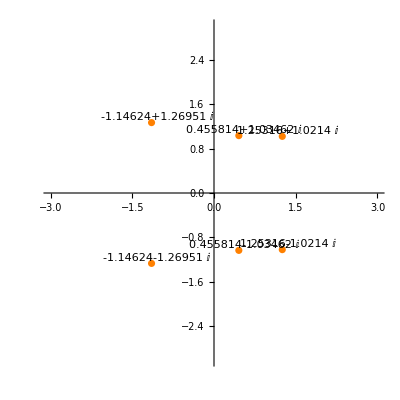

```mathematica
showPolyRootsComp[eqn1]
```

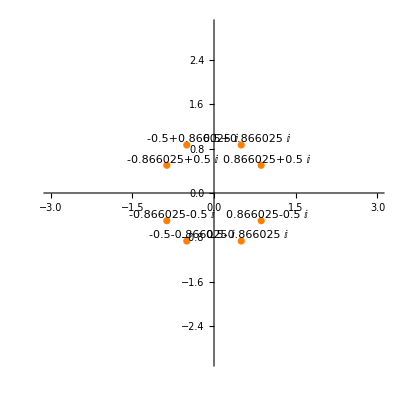

```mathematica
showPolyRootsComp[eqn2]
```

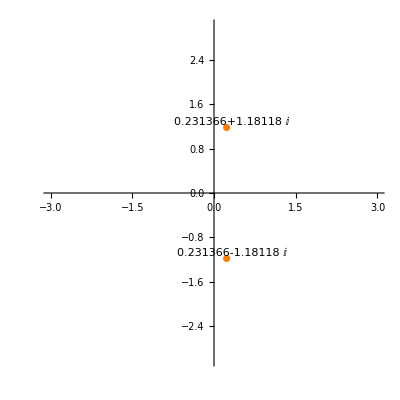

```mathematica
showPolyRootsComp[eqn4]
```

### Задача

График касательной к функции с помощью Manipulate.

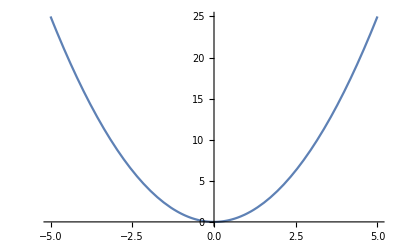

```mathematica
(*Уравнение касательной к графику функции y=f(x)*)
(*Сама функция*)
f1[x_]:=x^2
pl1=Plot[f1[x],{x,-5,5}]
```

```mathematica
kasat[f_,x0_]:=f[x0]+D[f[x],x]/.x->x0*(x-x0)//Expand
kasat[f1,4]
```

-16+8 x

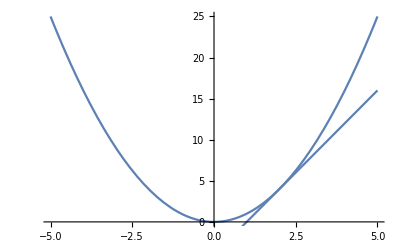

```mathematica
pl3=Plot[4+4 (-2+x),{x,-5,5}];
Show[pl1,pl3]
```

```mathematica
kasat[f1,5]
```

-25+10 x

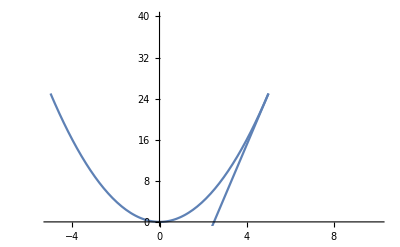

```mathematica
pl4=Plot[25+10 (-5+x),{x,-5,5}];
Show[pl1,pl4,PlotRange->{{-5,10},{0,40}}]
```

```mathematica
Manipulate[kasat[f1,a],{a,-5,5}]
```

```mathematica
Manipulate[Show[Plot[Evaluate@kasat[f1,a],{x,-5,5},PlotRange->{{-5,5},{-5,5}}],Plot[f1[x],{x,-5,5}]],{a,-5,5}]
```

```mathematica
ShowKasFun[f_]:=Manipulate[Show[Plot[Evaluate@kasat[f,a],{x,-5,5},PlotRange->{{-5,5},{-5,5}}],Plot[f1[x],{x,-5,5}]],{a,-5,5}]
```

```mathematica
ShowKasFun[f1]
```